```mathematica
(* This is to generate the phase diagram that appears in Fig. 1F in Meir and Wingreen *)
```

```mathematica
ClearAll["Global`*"];

(*Variables*)
vars={B,L1,L2,L12};

(*Equations of motion*)
eqs={S+B (1-(B+L1+L2+L12))-δ B-b (k L1+k L2+k L12) B/(B+L1+L2+L12), αL L1 (1-(B+L1+L2+L12))-δ L1+b (k L1+k/2 L12) B/(B+L1+L2+L12)-b L1 (k L2+k/2 L12)/(B+L1+L2+L12)-k L1, α L2 (1-(B+L1+L2+L12))-δ L2+b (k L2+k/2 L12) B/(B+L1+L2+L12)-k L2,  αL α L12 (1-(B+L1+L2+L12))-δ L12+  b (k L2+k/2 L12) L1/(B+L1+L2+L12)-k L12};

(*Jacobian matrix*)
Jac=D[eqs,{vars}];

(*Function to find stable fixed points*)
FindStableFixed[b_?NumericQ,α_?NumericQ,δ_?NumericQ,k_?NumericQ,S_?NumericQ]:=Module[{sols,valid,stable},(* Print[" eqs. b=",b," α=",α];*)sols=NSolve[Thread[eqs==0],vars];(* Print[" Sol:",sols];*)
valid=Select[sols,VectorQ[vars/. #,0<=#<=1&]&];
valid1=DeleteDuplicatesBy[valid,SortBy[Normal[#]/. x_Real:>Round[x,10^-8],First]&];
stable=Select[valid1,With[{eig=Eigenvalues[Jac/. #/. {αL->αL,b->b,δ->δ,k->k,S->S}]},AllTrue[Re[eig],#<0&]]&];
stable]

(*Classification*)
ClassifyFixed[sol_]:=Module[{vals,nonzero},vals=vars/. sol;
nonzero=Pick[vars,vals,_?(#>10^-6&)];
Which[nonzero==={B},1,nonzero==={B,L1},2,nonzero==={B,L2},3,nonzero==={B,L1,L2,L12},4,True,0]]

(*Parameters*)
S=0.001;δ=0.005;k=0.00004;αL=1;
(*Density plot in (b,αL2) plane*)
DensityPlot[Module[{fixed=FindStableFixed[b,α,δ,k,S],classes},classes=DeleteCases[ClassifyFixed/@fixed,0];
If[Length[classes]>1,Print[Length[classes]," solutions,  b=",b," α=",α]];
If[classes==={},0,First[classes]]],{b,0,200},{α,0.1,1},PlotPoints->10,PlotLegends->Placed[{"None","{B}","{B,L1}","{B,L2}","{B,L1,L2,L12}"},Right],ColorFunction->(Switch[Floor[#],0,Green,1,Orange,2,Red,3,Blue,_,Purple]&),ColorFunctionScaling->False,PlotLegends->None,FrameStyle->Directive[FontSize->16],FrameTicks->{{Table[{val,NumberForm[val,{2,1}]},{val,{0.2,0.4,0.6,0.8,1.0}}],None},(*y-axis with 1.0 instead of 1*){Table[{val,NumberForm[val,{4,1}]},{val,{0,50,100,150,200}}],None}    (*x-axis*)}]
```

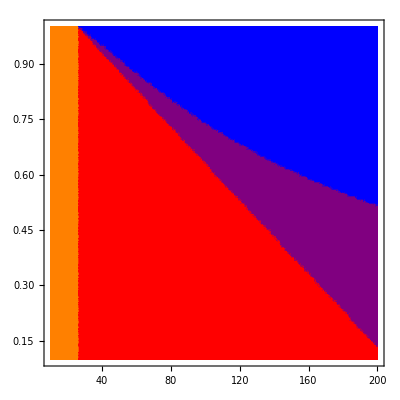

```mathematica
(* This is the time dependence, appearing in Fig. 1C*)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
Deqs={D[B[t],t]==S+B[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ B[t]-b (k L1[t]+k L2[t]+k L12[t]) B[t]/(B[t]+L1[t]+L2[t]+L12[t]), D[L1[t],t]==αL L1[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ L1[t]+b (k L1[t]+k/2 L12[t]) B[t]/(B[t]+L1[t]+L2[t]+L12[t])-b L1[t] (k L2[t]+k/2 L12[t])/(B[t]+L1[t]+L2[t]+L12[t])-k L1[t], D[L2[t],t]== α L2[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ L2[t]+b (k L2[t]+k/2 L12[t]) B[t]/(B[t]+L1[t]+L2[t]+L12[t])-k L2[t],  D[L12[t],t]==αL α L12[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ L12[t]+  b (k L2[t]+k/2 L12[t]) L1[t]/(B[t]+L1[t]+L2[t]+L12[t])-k L12[t],B[0]==B0,L1[0]==L10,L2[0]==L20,L12[0]==0};
```

```mathematica
NDSolve[Deqs/.{S->0.001,δ->0.005,k->0.00004,αL->0.8,b->100,α->0.8,B0->0.3,L10->0.6,L20->0.1},{B,L1,L2,L12},{t,0,25000}]
```

{{B→InterpolatingFunction[…],L1→InterpolatingFunction[…],L2→InterpolatingFunction[…],L12→InterpolatingFunction[…]}}

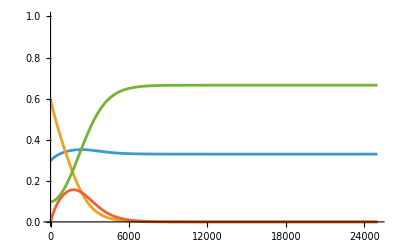

```mathematica
Plot[{Evaluate[B[t]/.%],Evaluate[L1[t]/.%],Evaluate[L2[t]/.%],Evaluate[L12[t]/.%]},{t,0,25000}, PlotRange->{0,1}]
```

```mathematica
(* To generate Fig.1D or E, just change the value of alpha above *)
```

```mathematica
(* =============================== *)
```

```mathematica
(* This is to calculate the phase diagram for the abortive defense system (Fig. 2A)*)
```

```mathematica
ClearAll["Global`*"];

(*Variables*)
vars={B,L1,L2,L12};

(*Equations of motion*)
eqs={S+B (1-(B+L1+L2+L12))-δ B-b (k L1+k L2+k L12) B/(B+L1+L2+L12), αL L1 (1-(B+L1+L2+L12))-δ L1+b (k L1+k/2 L12) B/(B+L1+L2+L12)-b L1 (k L2+k/2 L12)/(B+L1+L2+L12)-k L1, α L2 (1-(B+L1+L2+L12))-δ L2+b (k L2+k/2 L12) B/(B+L1+L2+L12)-b L2 (k L1+k/2 L12)/(B+L1+L2+L12)-k L2,  αL α L12 (1-(B+L1+L2+L12))-δ L12+  b (k L2+k/2 L12) L1/(B+L1+L2+L12)-k L12};

(*Jacobian matrix*)
Jac=D[eqs,{vars}];

(*Function to find stable fixed points*)
FindStableFixed[b_?NumericQ,α_?NumericQ,δ_?NumericQ,k_?NumericQ,S_?NumericQ]:=Module[{sols,valid,stable},(* Print[" eqs. b=",b," α=",α];*)sols=NSolve[Thread[eqs==0],vars,Method->"EndomorphismMatrix"];(* Print[" Sol:",sols];*)
valid=Select[sols,VectorQ[vars/. #,0<=#<=1&]&];
valid1=DeleteDuplicatesBy[valid,SortBy[Normal[#]/. x_Real:>Round[x,10^-8],First]&];
stable=Select[valid1,With[{eig=Eigenvalues[Jac/. #/. {αL->αL,b->b,δ->δ,k->k,S->S}]},AllTrue[Re[eig],#<0&]]&];
stable]

(*Classification*)
ClassifyFixed[sol_]:=Module[{vals,nonzero},vals=vars/. sol;
nonzero=Pick[vars,vals,_?(#>10^-6&)];
Which[nonzero==={B},1,nonzero==={B,L1},2,nonzero==={B,L2},3,nonzero==={B,L1,L2,L12},4,True,0]]

(*Parameters*)
S=0.001;δ=0.005;k=0.00004;αL=1;
(*Density plot in (b,αL2) plane*)
DensityPlot[Module[{fixed=FindStableFixed[b,α,δ,k,S],classes},classes=DeleteCases[ClassifyFixed/@fixed,0];
(* If[Length[classes]>1,Print[Length[classes]," solutions,  b=",b," α=",α]];*)
If[Length[classes]>1,If[Sort[classes]=={3,4},-1,If[Sort[classes]=={2,3},-2,-3]],If[classes==={},0,First[classes]]]],{b,0,200},{α,0.1,1.0},PlotPoints->150,PlotLegends->Placed[{"None","{B}","{B,L1}","{B,L2}","{B,L1,L2,L12}"},Right],ColorFunction->(Switch[Floor[#],-3,Brown,-2,LightGreen,-1,Yellow,0,Green,1,Orange,2,Red,3,Blue,_,Purple]&),ColorFunctionScaling->False,PlotLegends->None,FrameStyle->Directive[FontSize->16],FrameTicks->{{Table[{val,NumberForm[val,{2,1}]},{val,{0.2,0.4,0.6,0.8,1.0}}],None},(*y-axis with 1.0 instead of 1*){Table[{val,NumberForm[val,{4,1}]},{val,{0,50,100,150,200}}],None}    (*x-axis*)}]
```

-Graphics-

```mathematica
(* This part checks which of the solutions is reached from different starting point (Fig. 2C) *)
```

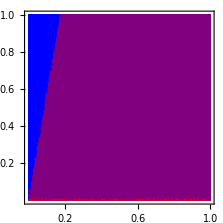

```mathematica
ClearAll["Global`*"];
vars={B,L1,L2,L12};
(*Equations of motion*)

Findsol[L10_,L20_,B0_,b_,α_,δ_,k_,S_,αL_]:=Module[{Deqs2,sol},Deqs2={D[B[t],t]==S+B[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ B[t]-b (k L1[t]+k L2[t]+k L12[t]) B[t]/(B[t]+L1[t]+L2[t]+L12[t]), D[L1[t],t]==αL L1[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ L1[t]+b (k L1[t]+k/2 L12[t]) B[t]/(B[t]+L1[t]+L2[t]+L12[t])-b L1[t] (k L2[t]+k/2 L12[t])/(B[t]+L1[t]+L2[t]+L12[t])-k L1[t], D[L2[t],t]== α L2[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ L2[t]+b (k L2[t]+k/2 L12[t]) B[t]/(B[t]+L1[t]+L2[t]+L12[t])-b L2[t] (k L1[t]+k/2 L12[t])/(B[t]+L1[t]+L2[t]+L12[t])-k L2[t],  D[L12[t],t]==αL α L12[t] (1-(B[t]+L1[t]+L2[t]+L12[t]))-δ L12[t]+  b (k L2[t]+k/2 L12[t]) L1[t]/(B[t]+L1[t]+L2[t]+L12[t])-k L12[t],B[0]==B0,L1[0]==L10,L2[0]==L20,L12[0]==0};
sol=
NDSolve[Deqs2,{B,L1,L2,L12},{t,0,250000}];{Evaluate[B[250000]/.sol],Evaluate[L1[250000]/.sol],Evaluate[L2[250000]/.sol],Evaluate[L12[250000]/.sol]}];
(*Classification*)
ClassifyFixed[vecsol_]:=Module[{vals,nonzero},
nonzero=Pick[vars,vecsol,_?(#>10^-6&)];
Which[nonzero==={B},1,nonzero==={B,L1},2,nonzero==={B,L2},3,nonzero==={B,L1,L2,L12},4,True,0]]
test=False;
(*Parameters*)
S=0.001;δ=0.005;k=0.00004;αL=1;b=180;α=0.95;B0=0.25;
(*Density plot in (b,αL2) plane*)
DensityPlot[Module[{vecsol=Flatten[Findsol[L10,L20,B0,b,α,δ,k,S,αL]],classes},If[test,Print[" L10=",L10," L20=",L20," vecsol=",vecsol]];
classes=ClassifyFixed[vecsol];If[test,Print[" classes=",classes]];
If[Length[classes]>1,Print[Length[classes]," solutions,  b=",b," α=",α]];
If[Length[classes]>1,-1,If[classes==={},0,classes]]],{L10,0,1},{L20,0,1},PlotPoints->50,PlotLegends->Placed[{"None","{B}","{B,L1}","{B,L2}","{B,L1,L2,L12}"},Right],ColorFunction->(Switch[Floor[#],-1,Yellow,0,Green,1,Orange,2,Red,3,Blue,4,Purple,_,Black]&),ColorFunctionScaling->False,PlotLegends->None,FrameStyle->Directive[FontSize->16],FrameTicks->{{Table[{val,NumberForm[val,{2,1}]},{val,{0.2,0.4,0.6,0.8,1.0}}],None},(*y-axis with 1.0 instead of 1*){Table[{val,NumberForm[val,{4,1}]},{val,{0.2,0.4,0.6,0.8,1.0}}],None}    (*x-axis*)}]
```

```mathematica
(* To generate  Fig. 2B, just change α in the above *)
```

```mathematica
(* ================================ *)
```

```mathematica
(* This is the phase diagram for a system including a phage that loses its defense system, Fig.3 in the paper *)
```

```mathematica
ClearAll["Global`*"];

(*Variables*)
vars={B,L1,L2,L2a,L12,L12a};

(*Equations of motion*)

eqs={S+B (1-(B+L1+L2+L2a+L12a+L12))-δ B-b(k L1+k L2a+k L2+ k L12+ k L12a)B/(B+L1+L2a+L12+L2+L12a), L1 (1-(B+L1+L2a+L2+L12+L12a))-δ L1 +b (k L1+k (1-β )L12+k (1-β )L12a)B/(B+L1+L2a+L2+L12+L12a)-b  L1(k L2+k L2a+β k L12+β k L12a)/(B+L1+L2a+L2+L12+L12a)-k L1,α L2 (1-(B+L1+L2a+L2+L12+L12a))-δ L2 +b( γ k L2+γ β k L12)B/(B+L1+L2a+L2+L12+L12a)(* -b L2(k L1+k  β L12)/(B+L1+L2+L12)*)-k L2,L2a (1-(B+L1+L2a+L2+L12+L12a))-δ L2a +b( k (1-γ) L2+k L2a+(1-γ) β k L12+ β k L12a)B/(B+L1+L2a+L2+L12+L12a)-b L2a(k L1+k  (1-β )L12+k  (1-β )L12a)/(B+L1+L2a+L2+L12+L12a)-k L2a,α L12 (1-(B+L1+L2a+L2+L12+L12a))-δ L12 +b(k γ L2+k  β γ L12)L1/(B+L1+L2a+L2+L12+L12a)-k L12  , L12a (1-(B+L1+L2a+L2+L12+L12a))-δ L12a  +b(k L1+k (1- β) L12+k (1- β) L12a)L2a/(B+L1+L2+L12+L12a)+b((1-γ)k L2+k L2a+(1-γ)k  β L12+k  β L12a)L1/(B+L1+L2a+L2+L12+L12a)-k L12a};
(*Jacobian matrix*)
Jac=D[eqs,{vars}];

(*Function to find stable fixed points*)
FindStableFixed[b_?NumericQ,α_?NumericQ,δ_?NumericQ,k_?NumericQ,S_?NumericQ,β_?NumericQ,γ_?NumericQ]:=Module[{sols,sol,valid,stable},(* Print[" eqs. b=",b," α=",α];*)(* sols=Solve[Thread[eqs==0],vars];*)
sol={};threshold=10^-7;
sol1=FindRoot[Thread[eqs==0],{{B,0.25},{L1,0.1},{L2,0.25},{L2a,0.25},{L12,0.1},{L12a,0.25}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
sol1=FindRoot[Thread[eqs==0],{{B,0.25},{L1,0.1},{L2,0},{L2a,0},{L12,0.0},{L12a,0}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
sol1=FindRoot[Thread[eqs==0],{{B,0.25},{L1,0.0},{L2,0.0},{L2a,0.2},{L12,0.0},{L12a,0}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
sol1=FindRoot[Thread[eqs==0],{{B,0.25},{L1,0.2},{L2,0.0},{L2a,0.2},{L12,0.0},{L12a,0.1}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
sol1=FindRoot[Thread[eqs==0],{{B,0.25},{L1,0},{L2,0.2},{L2a,0.2},{L12,0.0},{L12a,0.0}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
sol1=FindRoot[Thread[eqs==0],{{B,0.25},{L1,0},{L2,0},{L2a,0},{L12,0},{L12a,0}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
sol1=FindRoot[Thread[eqs==0],{{B,0.16},{L1,0.01},{L2,0.6},{L2a,0.1},{L12,0.04},{L12a,0.056}}];If[Norm[eqs/.sol1]<threshold,sol=Append[sol,sol1]];
ThresholdZero[list_]:=list/. x_/;Abs[x]<10^(-5)->0;
RemoveNearDuplicateSolutions[sols_,tol_:10^-6]:=Module[{vals},DeleteDuplicates[sols,(vals[#1]=Values[#1];vals[#2]=Values[#2];
Norm[vals[#1]-vals[#2]]<tol)&]];
sols=RemoveNearDuplicateSolutions[ThresholdZero[sol],10^-5];
(* Print[" Sol:",sols];*)
valid=Select[sols,VectorQ[vars/. #,-0.00001<=#<=1&]&];
stable=Select[valid,With[{eig=Eigenvalues[Jac/. #/. {α->α,b->b,δ->δ,k->k,S->S,β->β,γ->γ}]},AllTrue[Re[eig],#<0&]]&];
stable]

(*Classification*)
ClassifyFixed[sol_]:=Module[{vals,nonzero},vals=vars/. sol;
nonzero=Pick[vars,vals,_?(#>10^-6&)];
Which[nonzero==={B},1,nonzero==={B,L1},2,nonzero==={B,L2a},3,nonzero==={B,L1,L2a,L12a},4,nonzero==={B,L1,L2,L2a,L12,L12a},5,True,0]]

(*Parameters*)
S=0.001;δ=0.005;k=0.00004;β=1/2;γ=0.999;
(*Density plot in (b,αL2) plane*)
DensityPlot[Module[{fixed=FindStableFixed[b,α,δ,k,S,β,γ],classes},classes=DeleteCases[ClassifyFixed/@fixed,0];
If[classes==={},0,First[classes]]],{b,0,200},{α,0.65,1},PlotPoints->50,PlotLegends->Placed[{"None","{B}","{B,L1}","{B,L2a}","{B,L1,L2a,L12a}","{B,L1,L2,L2a,L12,L12a}"},Right],ColorFunction->(Switch[Floor[#],0,Green,1,Orange,2,Red,3,Blue,4,DarkGreen,5,Brown,_,Purple]&),ColorFunctionScaling->False,PlotLegends->None,AspectRatio->1/2,FrameStyle->Directive[FontSize->16],FrameTicks->{{Table[{val,NumberForm[val,{2,1}]},{val,{0.7,0.8,0.9,1.0}}],None},(*y-axis with 1.0 instead of 1*){Table[{val,NumberForm[val,{4,1}]},{val,{0,50,100,150,200}}],None}    (*x-axis*)}]
```

-Graphics-

```mathematica
(* Fig. 3 C and D are obtained by solving the time-dependent equation, as above, with the additional death term for L_2 *)
```

```mathematica
(* ============================= *)
```

```mathematica
(* Fig. 4A - Rock, paper, scissors system *)
```

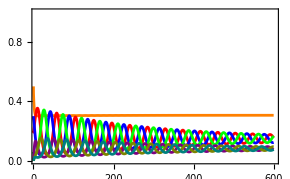
```mathematica
ClearAll[conds];
α1=0.9;
α2=0.75;
conds={αL1->α1,αL2->α1,αL3->α1,αL12->α2,αL13->α2,αL23->α2, S->0.001,δ->0.005,k->0.00004,κ->0.00001,b->100,B0->0.5,L20->0.3,L10->0.2,L30->0.06,L120->0.0,L130->0.0,L230->0.0,β->0.5,γ->0.9999};
maxt=150000;Sol1=NDSolve[{D[B[t],t]==S+B[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ B[t]-b k(L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t])B[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ),D[L1[t],t]==αL1 L1[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ L1[t] +b  k (L1[t]+β L12[t]+(1-β)L13[t])B[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-b  k L1[t](L3[t]+β  L13[t]+(1-β) L23[t])/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-k L1[t],D[L2[t],t]==αL2 L2[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ L2[t] +b  k (L2[t]+(1-β) L12[t]+β L23[t])B[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-b  k L2[t](L1[t]+  (1-β)L13[t]+ β L12[t])/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-k L2[t],D[L3[t],t]==αL3 L3[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ L3[t] +b  k (L3[t]+(1-β) L23[t]+β L13[t])B[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-b  k L3[t](L2[t]+(1-β)  L12[t]+ β L23[t])/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-k L3[t],D[L12[t],t]==αL12 L12[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ L12[t] +b k(L1[t]+ β L12[t]+(1-β)L13[t])L2[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-k L12[t], D[L13[t],t]==αL13 L13[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ L13[t] +b k(L3[t]+β  L13[t]+(1-β) L23[t])L1[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-k L13[t],D[L23[t],t]==αL23 L23[t] (1-(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]))-δ L23[t] +b k(L2[t]+(1-β) L12[t]+β L23[t])L3[t]/(B[t]+L1[t]+L2[t]+L3[t]+L12[t]+L13[t]+L23[t]+κ)-k L23[t]  ,B[0]==B0,L1[0]==L10,L2[0]==L20,L3[0]==L30,L12[0]==L120,L13[0]==L130,L23[0]==L230}/.conds,{B,L1,L2,L3,L12,L13,L23},{t,0,maxt},PrecisionGoal->20];
p06B=Plot[Evaluate[B[t]/.Sol1],{t,0,maxt},PlotStyle->Orange, PlotRange->{0,1}];
p06L1=Plot[Evaluate[L1[t]/.Sol1],{t,0,maxt},PlotStyle->Red, PlotRange->{0,1}];
p06L2=Plot[Evaluate[L2[t]/.Sol1],{t,0,maxt},PlotStyle->Blue, PlotRange->{0,1}];p06L3=Plot[Evaluate[L3[t]/.Sol1],{t,0,maxt},PlotStyle->Green, PlotRange->{0,1}];
segmentLength=300; (*Adjust this value to change the length*)
p06L12=Plot[Evaluate[L12[t]/.Sol1],{t,0,maxt},ColorFunction->(If[Mod[Floor[#1/segmentLength],2]==0,Red,Blue]&),ColorFunctionScaling->False,PlotRange->{0,1}];
p06L13=Plot[Evaluate[L13[t]/.Sol1],{t,0,maxt},ColorFunction->(If[Mod[Floor[#1/segmentLength],2]==0,Green,Red]&),ColorFunctionScaling->False,PlotRange->{0,1}];p06L23=Plot[Evaluate[L23[t]/.Sol1],{t,0,maxt},ColorFunction->(If[Mod[Floor[#1/segmentLength],2]==0,Green,Blue]&),ColorFunctionScaling->False,PlotRange->{0,1}];
fsize=18;
alternatingLegendEntry=Graphics[{{Red,AbsoluteThickness[2],Line[{{-0.5,-0.18},{-0.2,-0.18}}]},(*Red segment,length 0.5*){Green,AbsoluteThickness[2],Line[{{-0.2,-0.18},{-0.05,-0.18}}]},(*Blue segment,length 0.5*)Text[Style[Row[{"Double lysogen (",DisplayForm[OverscriptBox[ToBoxes[Subscript["L",12],StandardForm],AdjustmentBox[StyleBox["∼",FontSize->18,FontWeight->"Light"],BoxBaselineShift->2.0]]],")"}],FontSize->fontsize],{0.12,0},{-1,0}](*Label text,positioned*)},ImageSize->{200,30},(*Overall size of the legend entry*)PlotRange->{{-0.4,3.5},{-0.4,0.1}} (*Explicit plot range for tight control*)];
xTicks=Table[{t,Style[ToString[4 t/1000],FontSize->fsize]},(*label scaling*){t,0,maxt,50000}];
yTicks=Join[{{0.,"0.0"}},Table[{y,ToString@NumberForm[y,{2,1}]},{y,0.2,1.,0.2}]];
fontsize=14;
p06=Show[{p06B,p06L1,p06L2,p06L3,p06L12,p06L13,p06L23},LabelStyle->{FontSize->14},Frame->{{True,False},{True,False}},PlotRange->{{2000,maxt},{0,1}},FrameTicks->{{Table[{y,NumberForm[y,{2,1}]},{y,0.,1.,0.2}],None},(*y*){xTicks,None}}]
-Graphics-
```

```mathematica
(* Fig. 4B can be generated by changin α2 above *)
```